# 2D Causal Array

## Slice

```mathematica
mka[x_,y_, z_] := {{{x,y,z},{x+1,y,z}},
{{x,y,z},{x-1,y,z}},
{{x,y,z},{x,y+1,z}},
{{x,y,z},{x,y-1,z}},
{{x+1,y+1,z}, {x+1,y,z}},
{{x-1,y-1,z},{x-1,y,z}},
{{x+1,y+1,z}, {x,y+1,z}},
{{x-1,y-1,z}, {x,y-1,z}}
}
```

```mathematica
mka[x_,y_] := mka[x,y,{}]
```

```mathematica
array = Join[
mka[-6,-6], mka[-4,-6], mka[-2,-6],mka[0,-6],mka[2,-6],mka[4,-6],mka[6,-6],
mka[-6,-4], mka[-4,-4], mka[-2,-4],mka[0,-4 ],mka[2,-4],mka[4,-4],mka[6,-4],
mka[-6,-2], mka[-4,-2], mka[-2,-2],mka[0,-2],mka[2,-2],mka[4,-2],mka[6,-2],
mka[-6,0], mka[-4,0], mka[-2,0],mka[0,0],mka[2,0],mka[4,0],mka[6,0],
mka[-6,2], mka[-4,2], mka[-2,2],mka[0,2],mka[2,2],mka[4,2],mka[6,2],
mka[-6,4], mka[-4,4], mka[-2,4],mka[0,4],mka[2,4],mka[4,4],mka[6,4],
mka[-6,6], mka[-4,6], mka[-2,6],mka[0,6],mka[2,6],mka[4,6],mka[6,6]
]
```

{{{-6,-6,{}},{-5,-6,{}}},{{-6,-6,{}},{-7,-6,{}}},{{-6,-6,{}},{-6,-5,{}}},{{-6,-6,{}},{-6,-7,{}}},{{-5,-5,{}},{-5,-6,{}}},{{-7,-7,{}},{-7,-6,{}}},381,{{6,6,{}},{6,5,{}}},{{7,7,{}},{7,6,{}}},{{5,5,{}},{5,6,{}}},{{7,7,{}},{6,7,{}}},{{5,5,{}},{6,5,{}}}}
 |  |  |  |

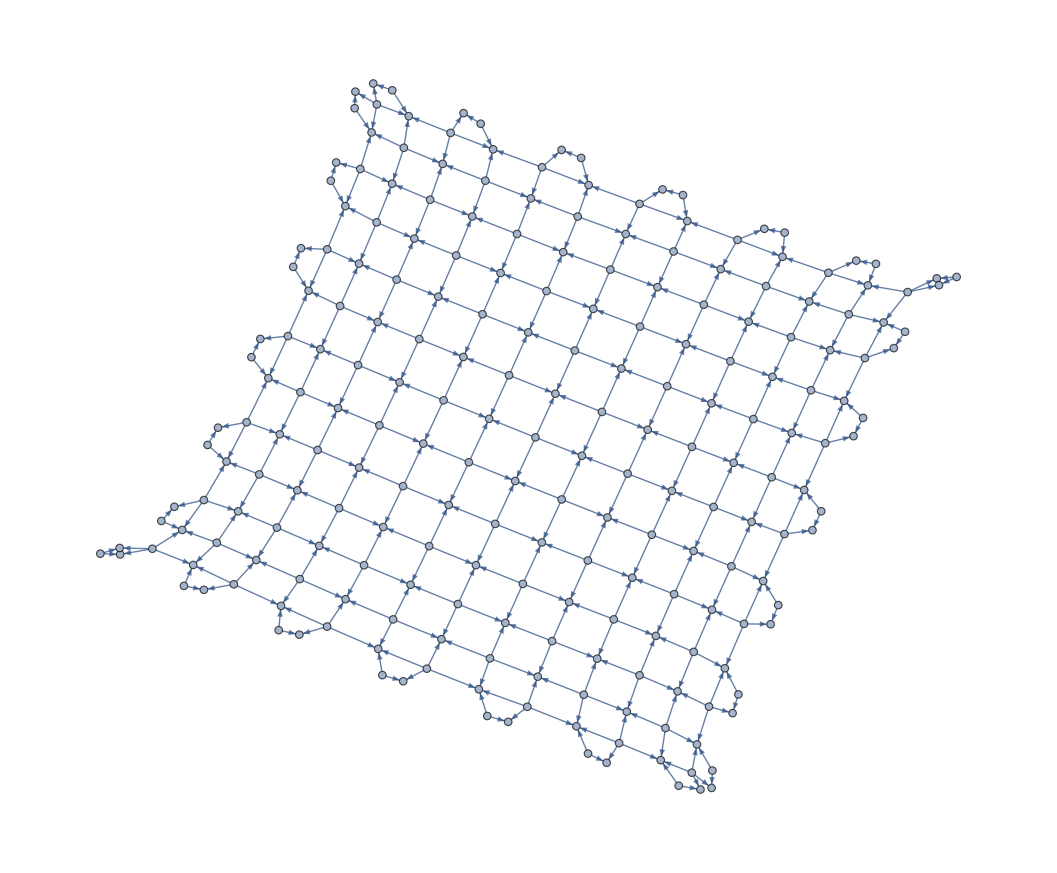

```mathematica
ResourceFunction["HypergraphToGraph"][array]
```

```mathematica
Rule1 = {{0,1},{0,2},{0,3},{0,4}} -> {{1,0},{2,0}, {3,0}, {4,0}}
```

{{0,1},{0,2},{0,3},{0,4}}→{{1,0},{2,0},{3,0},{4,0}}

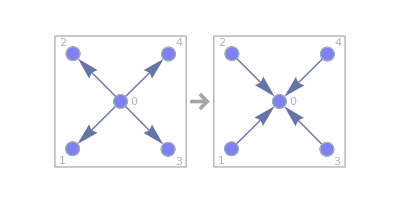

```mathematica
RulePlot[WolframModel[Rule1],VertexLabels->Automatic]
```

```mathematica
fa = WolframModel[Rule1,array,15,"FinalState"]
```

{{{-7,-7,{}},{-7,-6,{}}},{{-7,-7,{}},{-6,-7,{}}},{{-5,-7,{}},{-5,-6,{}}},{{-5,-7,{}},{-4,-7,{}}},{{-3,-7,{}},{-3,-6,{}}},{{-3,-7,{}},{-2,-7,{}}},381,{{0,2,{}},{0,1,{}}},{{0,-1,{}},{0,0,{}}},{{-1,0,{}},{0,0,{}}},{{1,0,{}},{0,0,{}}},{{0,1,{}},{0,0,{}}}}
 |  |  |  |

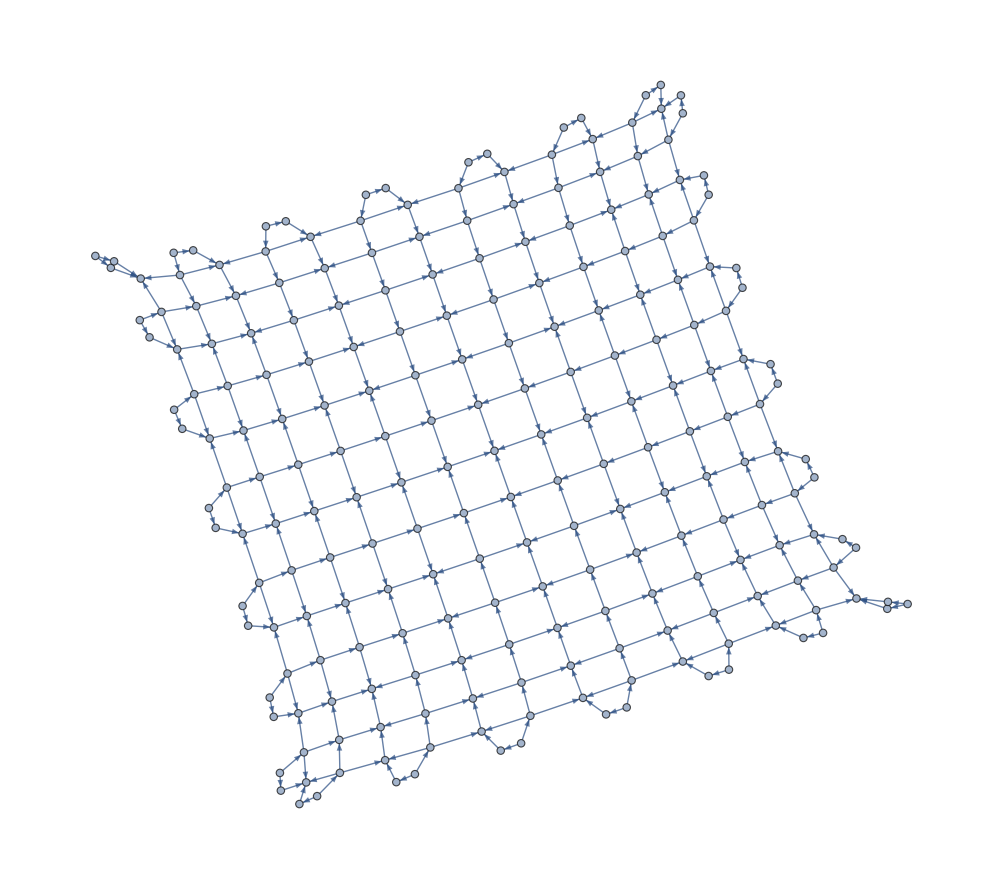

```mathematica
ResourceFunction["HypergraphToGraph"][fa]
```